# Introduction to Fractals and Holomorphic Dynamics in Mathematica

## Murphy Sünnenwold

Careful: Some of the used functions are rather new and only work in newer versions of Mathematica!
This is meant to be run from top to bottom in Mathematica 13

## Introduction

### Sierpinski Triangle

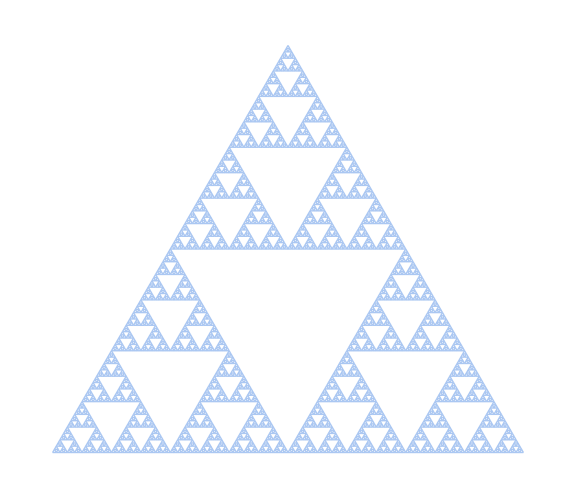

```mathematica
SierpinskiMesh[7, PlotTheme->"Lines", ImageSize->Large] (* Final version: ImageSize->{3000,3000} *)
```

## Fractals & Holomorphic Dynamics

## Utilities

```mathematica
(* returns the complex number from a x,y coordinate (opposite to ReIm) *)
XYtoC[c_]:=c[[1]]+c[[2]] I; 
(* performs "it" iterations of the quadratic map with parameter c and returns the x,y coordinates *)
quadraticMap[c_,z0_,it_]:=RecurrenceTable[{z[n+1]==(z[n])^2 +c,z[0]==0},z,{n,0,it}];
(* performs "it" iterations of the logistic map with parameter r and returns the x,y coordinates *)
logisticMap[r_,x0_,it_]:=RecurrenceTable[{x[n+1]==r x[n] (1-x[n]),x[0]==x0},x,{n,0,it}];
```

## Holomorphic Dynamics

### Holomorphic Function

```mathematica
hfCenter =50+50I;
hfNumPoints = 100;
hfDistance=5;
hfRange = {20,80};
hfColorFun[x_]:=Hue[x/80,1,0.9];
```

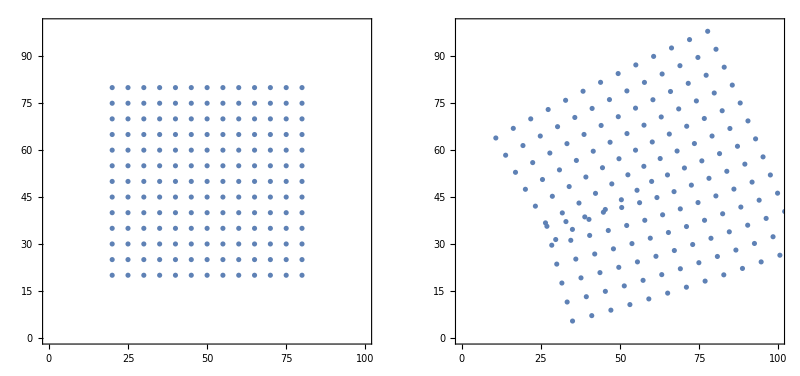

```mathematica
distributedPoints = XYtoC/@Flatten[CoordinateBoundsArray[{hfRange,hfRange}, hfDistance],1];
f[z_]:=(z-hfCenter)^1.05*E^(Pi/8 I)+hfCenter+10;
fI[z_] := InverseFunction[f][z];

GraphicsRow[{
ComplexListPlot[
distributedPoints,
Frame->True, PlotRange->{{0,100},{0,100}}, AspectRatio->1, ColorFunctionScaling->False,
ColorFunction->Function[{x,y,θ,r},hfColorFun[y]]
],
ComplexListPlot[
f/@distributedPoints,
Frame->True, PlotRange->{{0,100},{0,100}}, AspectRatio->1,ColorFunctionScaling->False, 
ColorFunction->Function[{x,y,θ,r},hfColorFun[N[ReIm[fI[XYtoC[{x,y}]]][[2]]]]]
]
}]
```

### Dynamic System

```mathematica
dynF[z_] := z*E^(Pi/2 * I);
dynZ = .8+.2I;
dynPoints=RecurrenceTable[{z[n+1]==dynF[z[n]], z[0]==dynZ},z,{n,0,3}];

Show[
ComplexListPlot[
Callout/@dynPoints, PlotRange->{{-1.1,1.1},{-1.1,1.1}},
AxesLabel->{"Re","Im"},Frame->True, PlotStyle->{Orange, PointSize[.016]}
],
Graphics[
{Lighter[Lighter[Green]],Dashed,Arrowheads[.02],
Table[Arrow[BezierCurve[ReIm/@With[{p =Table[dynPoints[[Mod[n+i,4]+1]],{i,0,1}]},Insert[p,.84*Total[p],2]]]],{n,1,4}]}
]
]
```

-Graphics-

## Fractal Geometry

### Fractal Dimension

#### Shapes (line, square, cube, Sierpinski triangle)

```mathematica
fdColor = RGBColor[84/255,147/255,255/255];
fdRange2={{-40,40},{-40,40}};
fdRange3 = {{-40,40},{-40,40}, {-40,40}};

line = Graphics[
{Text[Style["L, M", 14], {0,5}],fdColor,Thick, Line[{{-30,0},{30,0}}]}, 
PlotRange->fdRange2
];

square = Graphics[
{Text[Style["L, M", 14], {0,35}],fdColor,Rectangle[{-30,-30},{30,30}]}, 
PlotRange->fdRange2
];

cube = Graphics3D[
{Text[Style["L, M", 14], {0,0,40}],fdColor,Cube[60]}, 
PlotRange->fdRange3, 
Boxed->False,ViewPoint->{1,-3,1}, 
Lighting->"Neutral"
];

sierpinskiTriangle = Show[MeshRegion[SierpinskiMesh[6, DataRange->{{-30,30},{-30,30}}, ImageSize->Medium],MeshCellStyle->{{1,All}->fdColor}, PlotTheme->"Lines", PlotRange->fdRange2], Graphics[{Text[Style["L, M", 14], {0,35}]}]];

fg1 = GraphicsGrid[{{line, square},{cube, sierpinskiTriangle}},ImageSize->Large, Spacings->0]
```

-Graphics-

#### Shapes (scaled down)

```mathematica
line = Graphics[
{Text[Style["2x (sL, sM)", 14], {0,5}],fdColor,Thick, Line[{{-31,0},{-1,0}}], Line[{{31,0},{1,0}}]}, 
PlotRange->fdRange2
];

square = Graphics[
{Text[Style["4x (sL, s^2M)",14], {0,35}],fdColor,Rectangle[{-31,-31},{-1,-1}],Rectangle[{-31,1},{-1,31}],Rectangle[{1,1},{31,31}],Rectangle[{1,-1},{31,-31}]}, 
PlotRange->fdRange2
];

cube = Graphics3D[
{Text[Style["8x (sL, s^3M)",14], {0,0,40}],fdColor,Table[Cube[{x,y,z},30],{x,{-16,16}},{y,{-16,16}},{z,{-16,16}}]}, 
PlotRange->fdRange3, 
Boxed->False,ViewPoint->{1,-3,1}, 
Lighting->"Neutral"
];

sierpinskiTriangle = Show[
MeshRegion[SierpinskiMesh[5, DataRange->{{-31,-1},{-31,-1}}],MeshCellStyle->{{1,All}->fdColor},PlotTheme->"Lines"],
MeshRegion[SierpinskiMesh[5, DataRange->{{-15,15},{1,31}}],MeshCellStyle->{{1,All}->fdColor},PlotTheme->"Lines"],
MeshRegion[SierpinskiMesh[5, DataRange->{{1,31},{-31,-1}}],MeshCellStyle->{{1,All}->fdColor},PlotTheme->"Lines"],
Graphics[{Text[Style["3x (sL, s^log_2M)",14], {0,35}]}],
PlotRange->fdRange2
];

fg2 = GraphicsGrid[{{line, square},{cube, sierpinskiTriangle}},ImageSize->Large, Spacings->0]
```

-Graphics-

#### Combined

```mathematica
GraphicsRow[{fg1,fg2}, ImageSize->Full, Spacings->10, ImagePadding->0,PlotRangePadding->0, Dividers->Center]
```

-Graphics-

### Identifying Fractals

Minkowski dimension (box-counting dimension) -  Based on:  https://community.wolfram.com/groups/-/m/t/1025046

#### Utility

```mathematica
overlayGrid[img_, s_]:=Overlay[{img,Graphics[{},GridLines->{Subdivide[-1, 1,ImageDimensions[img][[1]]/s],Subdivide[-1, 1,ImageDimensions[img][[2]]/s]},
PlotRangePadding->None,GridLinesStyle->Directive[Gray]]}];
```

#### Box counting

Importing & Preprocessing

```mathematica
image=Import["https://maps-germany-de.com/img/0/germany-map-outline.jpg"];
{imW,imH}=ImageDimensions[image];
{imWdiv,imHdiv}=Divisors/@ImageDimensions[image];
```

```mathematica
(* Tweak size for many common divisors *)
{imW,imH}={1260 , 1800}(*If[Length[imWdiv]>Length[imHdiv],Join[{imW},Nearest[imWdiv,imH]],Join[Nearest[imHdiv,imW],{imH}]]*)
{imWdiv,imHdiv}=Divisors/@{imW,imH};
image=ImageResize[image,{imW,imH}];
imBinary=LocalAdaptiveBinarize[image,4,{0.9,0,0}];
GraphicsRow[{image,imBinary},ImageSize->600]
```

{1260,1800}

-Graphics-

Calculating N

1.23899+1.20992 x

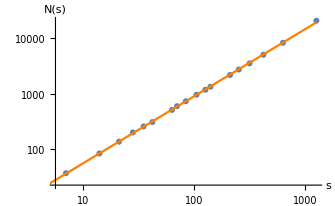

```mathematica
imGridSizes=Reverse[Intersection@@{imWdiv,imHdiv}];
imN={imW/#,Last@First@ImageLevels@Image[BlockMap[Min,ImageData[imBinary],{#,#}],"Bit"]}&/@imGridSizes;

imFit=LinearModelFit[Log[imN],{1,x},x];
imFit["BestFit"]
Show[ListLogLogPlot[imN, AxesLabel->{"s","N(s)"}],Plot[imFit[x],{x,0,Log[Last[(imW/#&/@imGridSizes)]]}, PlotStyle->Orange], ImageSize->Medium]
```

Images with overlay

```mathematica
imOverlay=ColorReplace[
ColorConvert[Image[BlockMap[Min,ImageData[image],{#,#}],"Bit"], "RGB"], 
{Black->RGBColor[0.85,0.97,0.05,0.5], White->RGBColor[0,0,0,0]}]&/@ imGridSizes;
imOverlay=ImageResize[#,{imW, imH},Resampling->"Nearest"]&/@imOverlay;
imBoxImages = Overlay[{image, #}, ImageSize->Large]&/@ imOverlay;
```

```mathematica
Manipulate[imBoxImages[[i]],{i,1,Length[imBoxImages],1}]
```

Part::partd: Part specification imBoxImages⟦16⟧ is longer than depth of object.

wefw

wefw

sdfsdf

sdfsdf

sdfasdfsa

sdfsdfsdfkjlhhhhhhhhhhhhhhhhhhhhhhhh’’
skdjfhskdjfh

sdlfkjsdlfkj
sldkfjs

## Fractals

### The Mandelbrot set & Julia sets

#### Utility

```mathematica
(* Function definitions *)
lines[x_]:={mbLineColor,Line[x]}; (* creates a Line graphic connecting the coordinates in x *)
points[x_] :={mbPointColor, Point[x]}; (* creates a Point graphic with points at the coordinates of x *)

(* creates a plot of the mandelbrot set with "it" number of iterations per point and an image resolution of "res" (also prints the time it took) *)
mandelbrotPlot[it_, res_] :=Block[{r},
r= Timing[
MandelbrotSetPlot[
{mbBottomLeft,mbTopRight},
MaxIterations->it,ImageResolution->res, 
Frame->True, ColorFunction->"Rainbow", (* Rainbow, SunsetColors *)
PerformanceGoal->"Quality",ImageSize->Large, PlotRangePadding->None]
];Print[r[[1]]];r[[2]]
];

(* creates a plot of the julia set for "c" with "it" number of iterations per point and an image resolution of "res" (also prints the time it took) *)
juliaPlot[c_,it_,res_]:=Block[{r},
r= Timing[
JuliaSetPlot[c,
MaxIterations->it,ImageResolution->res, 
Frame->True, ColorFunction->"Rainbow", (* Rainbow, SunsetColors *)
PerformanceGoal->"Quality",ImageSize->{Automatic,Large}, PlotRangePadding->None]
];Print[r[[1]]];r[[2]]
];
```

#### Parameters

```mathematica
(* Plot parameters *)
mbLineColor=Gray;
mbPointColor=Yellow;
mbBottomLeft =-1.8-1.15I;
mbTopRight=.5+1.15I;
mbRange={{Re[mbBottomLeft], Re[mbTopRight]},{Im[mbBottomLeft], Im[mbTopRight]}};
(* preload mandelbrot plot *)
mandelbrot=mandelbrotPlot[200,2000];
```

3.76563

#### Mandelbrot set - Full Image

```mathematica
mandelbrotPlot[150,1000] (* Final version: 150, 10000 (takes very long) *)
```

0.9375

-Graphics-

#### Mandelbrot set - Interactive

Drag around the yellow dot!

```mathematica
msInteractiveIt=50;
interactiveMandelbrotIteration =LocatorPane[
Dynamic[c],
Show[
mandelbrot,
Graphics[Dynamic[Join[
{Text[NumberForm[XYtoC[c],2],c +{0,0.05}, BaseStyle->Yellow]},
lines[ReIm/@Select[quadraticMap[XYtoC[c],0, msInteractiveIt],Abs[#]<20&]],
points[ReIm/@Select[quadraticMap[XYtoC[c],0, msInteractiveIt],Abs[#]<20&]]
]]],
PlotRange->mbRange, ImageSize->800
],Appearance->{Graphics[{Yellow, PointSize[Large], Point[{0,0}]}]}
]
```

```mathematica
(* create a snapshot of the current state of the interactive plot *)
Rasterize[interactiveMandelbrotIteration, ImageSize->Full]
```

#### Mandelbrot set & Julia set

```mathematica
(* Plot parameters *)
msStaticIt=100;
msStaticC=-0.5+0.5I;
```

```mathematica
(* Prerender julia plot*)
matchingJuliaPlot=juliaPlot[msStaticC,80,1000];
```

2.65625

```mathematica
mandelbrotIteration =Show[
mandelbrot, (* Final version: mandelbrotPlot[80,4000] *)
Graphics[Join[
lines[ReIm/@Select[quadraticMap[msStaticC,0, msInteractiveIt],Abs[#]<20&]],
points[ReIm/@Select[quadraticMap[msStaticC,0, msInteractiveIt],Abs[#]<20&]]
]],PlotRange->mbRange
];

GraphicsRow[{mandelbrotIteration,matchingJuliaPlot}, ImageSize->Full, Spacings->2]
```

-Graphics-

### Newton Fractals

#### Utility

```mathematica
newtonRaphsonStep[f_,z_]:=z-f[z]/f'[z];

(* Generates the plot of a newton fractal with a given resolution and function in [-2,2]x[-2i,2i]*)
newtonPlot[step_, f_]:=Block[{r},
r= Timing[
ListDensityPlot[
Arg@FixedPoint[newtonRaphsonStep[f,#]&,#]&/@Table[i+j I,{j,-2.,2.,step},{i,-2.,2.,step}],
ColorFunction->"Rainbow", FrameLabel->{"Re","Im"}, Frame->True, DataRange->{{-2,2},{-2,2}}, ImageSize->Large
]];Print[r[[1]]];r[[2]]
];
```

#### Newton fractal for given function

```mathematica
nfF[z_]:=z^3-1; (* Enter holomorphic function here *)
newtonFractal = newtonPlot[0.0081, nfF]; (* Final version: 0.0031 takes about 40 sec*)
```

5.29688

```mathematica
Show[
newtonFractal,
ComplexListPlot[
Callout[#,#, Background->None, Appearance->None,LabelStyle->{12,LightBlue}]&/@(z/.Solve[nfF[z]==0,z]),
PlotStyle->{LightBlue, PointSize[.01]}
]
]
```

-Graphics-

### The bifurcation diagram of the logistic map

#### Different values of r

```mathematica
lmNIt=1000;
lmWindowSize=100;
lmStep=0.001;
(* values of the logistic map *)
Manipulate[ListLinePlot[logisticMap[r,.5, lmNIt],PlotRange->{{w,lmWindowSize+w},{0,1}}],{r,lmStep,4,lmStep},{w,0,lmNIt-lmWindowSize,1}]
```

Example 1: r = 1.6, fix point

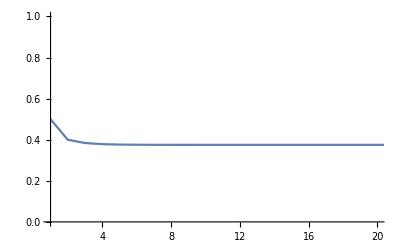

{0.375,0.375,0.375,0.375}

```mathematica
it1 = 20;
r1 = 1.6;
ListLinePlot[logisticMap[r1,.5, it1],PlotRange->{{1,it1},{0,1}}]
logisticMap[r1,.5, it1][[-4;;-1]]
```

Example 2: r = 3.4, two-cycle

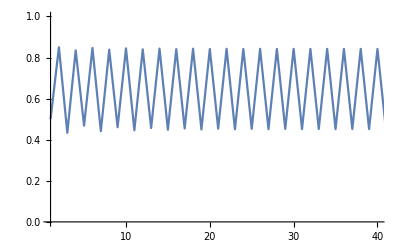

{0.842212,0.451829,0.842111,0.452065}

```mathematica
it2 = 40;
r2 = 3.4;
ListLinePlot[logisticMap[r2,.5, it2],PlotRange->{{1,it2},{0,1}}]
logisticMap[r2,.5, it2][[-4;;-1]]
```

Example 3: r = 3.5, four-cycle

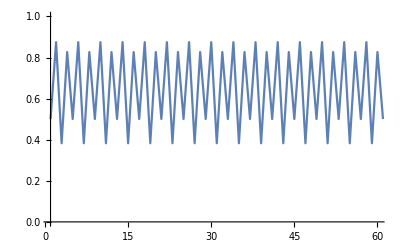

{0.500884,0.874997,0.38282,0.826941,0.500884}

```mathematica
it3 = 60;
r3 = 3.5;
ListLinePlot[logisticMap[r3,.5, it3],PlotRange->{{1,it3},{0,1}}]
logisticMap[r3,.5, it3][[-5;;-1]]
```

Example 4: r = 3.6, chaos

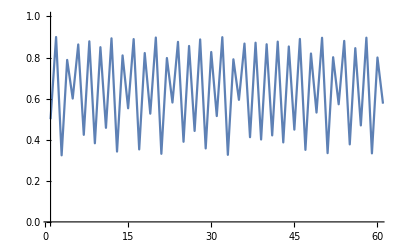

{0.469611,0.896676,0.333535,0.800242,0.575478}

```mathematica
it4 = 60;
r4 = 3.6;
ListLinePlot[logisticMap[r4,.5, it4],PlotRange->{{1,it4},{0,1}}]
logisticMap[r4,.5, it4][[-5;;-1]]
```

#### Full bifurcation diagram

```mathematica
lmfInterval=Range[0.001,4,0.001]; (* Final version: 0.0002, 400, 50 *)
lmfNumIterations =400; (* number of iterations to calculate *)
lmfNumToPlot=50; (* amout of the last iterations to plot *)
lmfPoints = Flatten[Table[Map[Prepend[#,i]&,Take[({#})&/@logisticMap[i,.5,lmfNumIterations],-lmfNumToPlot]],{i,lmfInterval}],1];
Length[lmfPoints]
```

200000

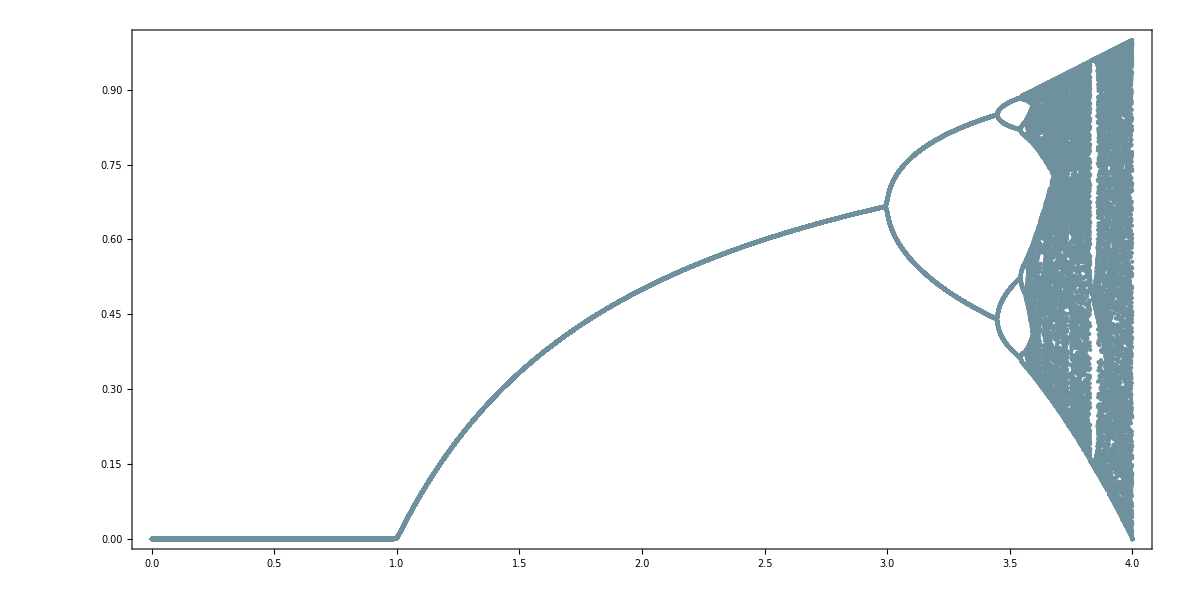

```mathematica
ListPlot[lmfPoints, PlotStyle->Directive[PointSize[Tiny], RGBColor["#6F919E"]], ImageSize->1200, Frame->True , AspectRatio->1/2]
```

#### Close-up bifurcation diagram

```mathematica
lmInterval=Range[2.9,4,0.001]; (* Final version: 0.00008, 600, 50 *)
lmNumIterations =600; (* number of iterations to calculate *)
lmNumToPlot=50; (* amout of the last iterations to plot *)
lmPoints = Flatten[Table[Map[Prepend[#,i]&,Take[({#})&/@logisticMap[i,.5,lmNumIterations],-lmNumToPlot]],{i,lmInterval}],1];
Length[lmPoints]
```

55050

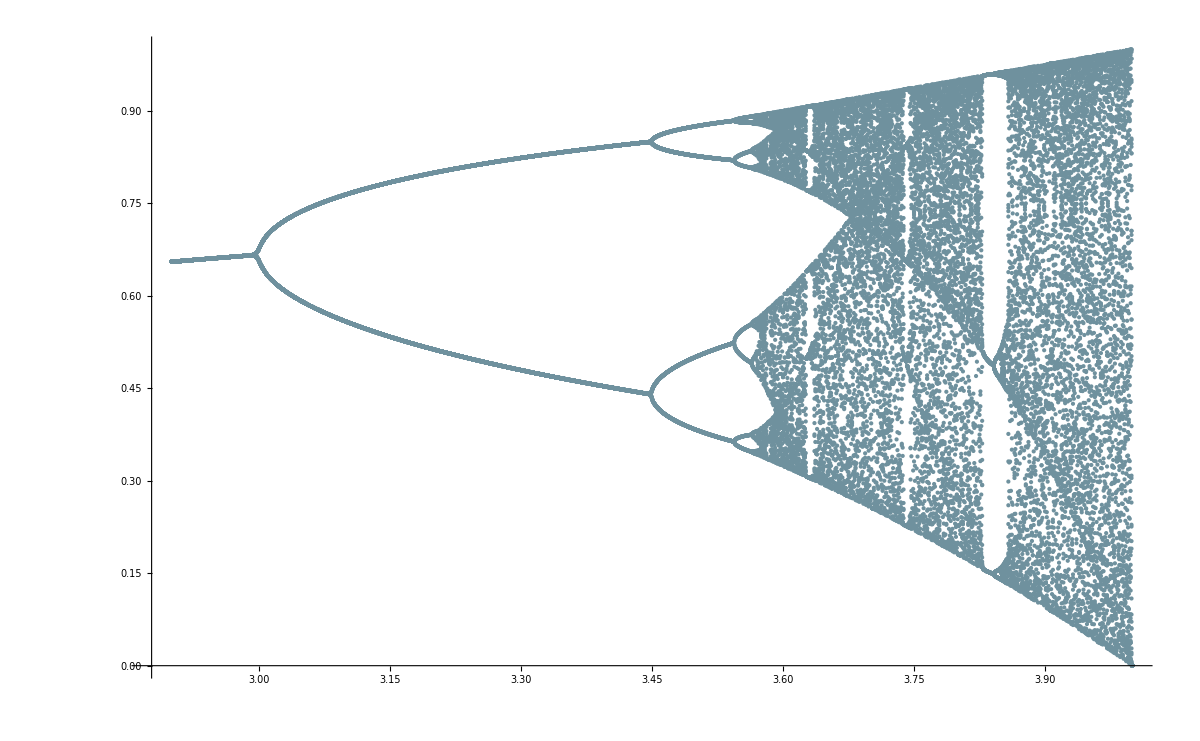

```mathematica
ListPlot[lmPoints, PlotStyle->Directive[PointSize[Tiny], RGBColor["#6F919E"]], ImageSize->1200]
```

## The logistic map in the Mandelbrot set

### The Mandelbrot set in 3D

```mathematica
Off[MandelbrotSetMemberQ::maxiter]; (* Turns off the warning *)
```

Parameters

```mathematica
(* Final version: 0.005, 400, 20 *)
ms3Dstep=0.01; 
(* number of iterations to calculate *)
ms3DnumIterations =100; 
(* amout of the last iterations to plot *)
ms3DnumToPlot=20;
```

Plotting the Mandelbrot set to test the parameters

```mathematica
(* the mandelbrot set with the given range and step (to fine tune)*)
ArrayPlot[Table[Boole[MandelbrotSetMemberQ[XYtoC[{x,y}], MaxIterations->800]],{y,-.9,.9,ms3Dstep},{x,-2,.4,ms3Dstep}]]
```

-Graphics-

```mathematica
(* All the points in the mandelbrot set with the given resolutiong (step size)*)
ms3DpointsInSet=Select[Flatten[Table[{x,y},{x,-2,.4,ms3Dstep},{y,-.9,.9,ms3Dstep}],1],MandelbrotSetMemberQ[XYtoC[#], MaxIterations->800]&];
Length[ms3DpointsInSet]
(* Mapping the points in the set to a third dimension (in this case using the real value of the last few iteration steps)*)
ms3Dpoints=Block[{r},
r= Timing[
Flatten[ Table[Map[Join[i,{Re[#]}]&,Take[quadraticMap[XYtoC[i],0,ms3DnumIterations],-ms3DnumToPlot]],{i, ms3DpointsInSet}],1]
];Print[r[[1]]];r[[2]]
];
Length[ms3Dpoints]
```

15140

4.25

302800

```mathematica
mandelbrot3DPlot=ListPointPlot3D[ms3Dpoints, PlotRange->{{-2,.4},{-.9,.9},{-2.5,2.5}}, Axes->True, AxesLabel->{"Re","Im", "Re[z_n]"},Boxed->True,BoxRatios->{Automatic,Automatic,1.6}, ImageSize->1000]
```

-Graphics3D-

Top-down view

```mathematica
Show[mandelbrot3DPlot, Axes->False, ViewPoint->{0,0,Infinity}, ImageSize->800]
```

-Graphics3D-

Side view

```mathematica
Show[mandelbrot3DPlot,Axes->False, ViewPoint->{0,Infinity,0}, ViewVertical->{0, 0, -1}, ImageSize->800]
```

-Graphics3D-

Slice at Im = 0

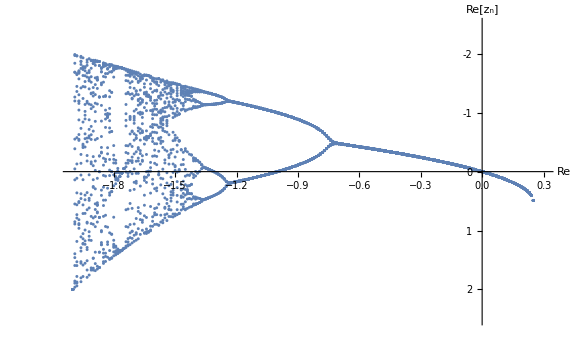

```mathematica
ListPlot[Select[ms3Dpoints, (#[[2]]==0)&][[All, {1,3}]],PlotRange->{{-2,.3},{-2.5,2.5}}, ScalingFunctions->"Reverse", ImageSize->Large, AxesLabel->{"Re", "Re[z_n]"}]
```

## Conclusion

#### Mandelbrot - Artistic with MandelbrotSetRemap

```mathematica
MSR=ResourceFunction["MandelbrotSetRemap"];
msrImageSize = {1000,500}; (* Final version: 2000, 1000 *)
msrOrigin = -.836+.229I;
```

```mathematica
layer1=MSR[msrOrigin,130,
MaxIterations->32,ImageSize->msrImageSize,
ColorFunction->ColorData["ValentineTones"],"MappingFunction"->"ModTrailings"];
layer2=MSR[msrOrigin,130,
MaxIterations->28,ImageSize->msrImageSize,
ColorFunction->ColorData[{"CherryTones","Reverse"}],"MappingFunction"->"LineOrbitTrap"];
combo=ImageAdjust[ImageDifference[layer1,layer2]];
Lighter[ImageMultiply[combo,
ImageAdjust[
ImageAdjust[
DerivativeFilter[ColorConvert[combo,"Grayscale"],{0,1},4]
],{.5,.3}]
]]
```

-Graphics-

#### Mandelbrot - close-up

```mathematica
(* Center: -.836+.229I *)
mandelbrotSetArt =AbsoluteTiming[MandelbrotSetPlot[
{-.850+.190I,-.810+.220I},
MaxIterations->800,ImageResolution->1000, (* Final version: 800, 8000 takes about 75 sec *)
Frame->False, ColorFunction->"Rainbow",
PerformanceGoal->"Quality",ImageSize->Full, PlotRangePadding->None
]];

mandelbrotSetArt[[1]]
mandelbrotSetArt[[2]]
```

1.13165

-Graphics-

#### Julia set

```mathematica
juliaSetArt=AbsoluteTiming[
JuliaSetPlot[-0.512511498387847167+0.521295573094847167I,
Frame->False,MaxIterations->800,  ImageResolution->1000, (* Final version: 800, 4000 takes about 60 sec *)
PerformanceGoal->"Quality", ColorFunction->"BlueGreenYellow", PlotRangePadding->None, ImageSize->Full]
];
juliaSetArt[[1]] 
juliaSetArt[[2]]
```

3.353

-Graphics-